```mathematica
Det[{{2,-1,0},{-1,-2,-1},{0,-1,2}}]
```

-12

```mathematica
Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==6]&]
```

{29525,29527,29533,29551,29605,29767,30253,31711,36085,49207}

```mathematica
g=allGraphs[quad1Key,"graph"]
```

-Graphics-

```mathematica
ga=AdjacencyMatrix[g];MatrixForm[ga]
```

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

```mathematica
DegreeMatrix[g_]:=Block[{},
Table[
Table[If[v1==v2,VertexDegree[g,v1],0],{v1,VertexList[g]}],{v2,VertexList[g]}
]
]
```

```mathematica
gd=DegreeMatrix[g]
```

{{3,0,0,0},{0,3,0,0},{0,0,3,0},{0,0,0,3}}

```mathematica
lm=gd-ga;MatrixForm[lm]
```

(3 | -1 | -1 | -1
-1 | 3 | -1 | -1
-1 | -1 | 3 | -1
-1 | -1 | -1 | 3)

```mathematica
Rest[Map[Rest,lm]]//Det
```

16

```mathematica
Det[lm]
```

0

```mathematica
Table[k->With[{g=allGraphs[k,"graph"]},Det[Rest[Map[Rest,DegreeMatrix[g]-AdjacencyMatrix[g]]]]],{k,nullAtomKeys}]
```

{0→0,1→0,3→0,9→0,13→0,27→0,36→0,81→0,84→0,109→0,243→0,244→0,273→0,333→0,364→0,729→0,738→0,810→0,972→0,1062→0,2187→0,2190→0,2214→0,2430→0,2460→0,2917→0,3160→0,6561→0,6562→0,6588→0,6642→0,6670→0,7293→0,7374→0,8757→0,8784→0,9490→0,19683→0,19684→0,19686→0,19692→0,19696→0,20439→0,20448→0,21951→0,21954→0,22708→0,26487→0,26488→0,27246→0,28764→0,29524→125}

```mathematica
TableForm[Table[With[{g=EmbedGraphInPlantri8[allGraphs,k]},Det[Rest[Map[Rest,DegreeMatrix[g]-AdjacencyMatrix[g]]]]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//FactorInteger, TableDepth->2]
```

{2,2} | {19,1} | {23,1} | {135533,1} |  | 
{3,3} | {7,1} | {727,1} | {1823,1} |  | 
{2,8} | {3,2} | {5,1} | {17,1} | {19,1} | {71,1}
{3,3} | {7,1} | {727,1} | {1823,1} |  | 
{2,2} | {19,1} | {23,1} | {135533,1} |  |

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs,gamma1Key],4]
```

0

```mathematica
FactorInteger[With[{g=Graph[plantri[[8]]]},Det[Rest[Map[Rest,DegreeMatrix[g]-AdjacencyMatrix[g]]]]]]
```

{{2,3},{3,1},{5,1},{29,1},{41,1},{109,1},{911,1}}

```mathematica
TableForm[Table[{allGraphs[k,"graph"],FactorInteger[With[{g=EmbedGraphInPlantri8[allGraphs,k]},Det[Rest[Map[Rest,DegreeMatrix[g]-AdjacencyMatrix[g]]]]]]},{k,atomKeys}], TableDepth->2]
```

-Graphics- | {{7,1},{17,1},{61,1},{191,1},{6211,1}}
-Graphics- | {{13,1},{19,1},{269,1},{12263,1}}
-Graphics- | {{3,2},{11,1},{17,1},{53,1},{13931,1}}
-Graphics- | {{7,2},{53,1},{463,1},{659,1}}
-Graphics- | {{2,4},{3,1},{2122963,1}}
-Graphics- | {{3,1},{13,1},{17,1},{41,1},{181,1},{263,1}}
-Graphics- | {{2,7},{3,3},{5,1},{7,1},{1423,1}}
-Graphics- | {{3,2},{11,1},{17,1},{53,1},{13931,1}}
-Graphics- | {{2,8},{3,2},{5,1},{17,1},{19,1},{71,1}}
-Graphics- | {{2,6},{2582947,1}}
-Graphics- | {{13,1},{19,1},{269,1},{12263,1}}
-Graphics- | {{2,4},{3,1},{5,1},{7,1},{13,1},{71,2}}
-Graphics- | {{2,6},{2582947,1}}
-Graphics- | {{2,4},{3,1},{2122963,1}}
-Graphics- | {{3,3},{5,1},{19,1},{73,1},{109,1}}
-Graphics- | {{2,4},{7,1},{7338013,1}}
-Graphics- | {{23,1},{157,1},{29399,1}}
-Graphics- | {{2,2},{42806087,1}}
-Graphics- | {{47,1},{2360021,1}}
-Graphics- | {{673,1},{32257,1}}
-Graphics- | {{7,1},{1097,1},{148471,1}}
-Graphics- | {{2,2},{19,1},{23,1},{135533,1}}
-Graphics- | {{3,3},{7,1},{727,1},{1823,1}}
-Graphics- | {{2,2},{3,1},{17,1},{127,1},{5879,1}}
-Graphics- | {{50004839,1}}
-Graphics- | {{2,6},{3,1},{513053,1}}
-Graphics- | {{2,2},{7,2},{179,1},{593,1}}
-Graphics- | {{7,1},{1097,1},{148471,1}}
-Graphics- | {{2,2},{3,1},{17,1},{127,1},{5879,1}}
-Graphics- | {{3,3},{7,1},{727,1},{1823,1}}
-Graphics- | {{2,2},{19,1},{23,1},{135533,1}}
-Graphics- | {{50004839,1}}
-Graphics- | {{2,2},{47,1},{89,1},{8837,1}}
-Graphics- | {{2,2},{3,2},{727,1},{1901,1}}
-Graphics- | {{2,1},{5,1},{7,1},{29,1},{73,1},{887,1}}
-Graphics- | {{2,6},{3,1},{5,1},{17,1},{19,1},{149,1}}
-Graphics- | {{2,2},{3,1},{19,1},{74017,1}}
-Graphics- | {{2,4},{7,1},{7338013,1}}
-Graphics- | {{47,1},{2360021,1}}
-Graphics- | {{2,2},{42806087,1}}
-Graphics- | {{23,1},{157,1},{29399,1}}
-Graphics- | {{673,1},{32257,1}}
-Graphics- | {{3,1},{7,3},{41,1},{2609,1}}
-Graphics- | {{2,6},{3,4},{31,1},{139,1}}
-Graphics- | {{2,2},{47,1},{89,1},{8837,1}}
-Graphics- | {{2,2},{3,2},{727,1},{1901,1}}
-Graphics- | {{3,1},{6618839,1}}
-Graphics- | {{2,6},{3,1},{513053,1}}
-Graphics- | {{2,2},{7,2},{179,1},{593,1}}
-Graphics- | {{3,1},{6618839,1}}
-Graphics- | {{2,2},{3,1},{19,1},{74017,1}}
-Graphics- | {{2,1},{3,5},{29,1},{281,1}}

```mathematica
TableForm[Table[{allGraphs[k,"graph"],With[{g=allGraphs[k,"graph"]},NumberOfSpanningTrees[g]]},{k,atomKeys}], TableDepth->2]
```

Det::matsq: Argument {} at position 1 is not a non-empty square matrix.

-Graphics- | 125
-Graphics- | 16
-Graphics- | 16
-Graphics- | 16
-Graphics- | 3
-Graphics- | 16
-Graphics- | 3
-Graphics- | 16
-Graphics- | 3
-Graphics- | 3
-Graphics- | 16
-Graphics- | 3
-Graphics- | 3
-Graphics- | 3
-Graphics- | 1
-Graphics- | 16
-Graphics- | 3
-Graphics- | 3
-Graphics- | 3
-Graphics- | 1
-Graphics- | 16
-Graphics- | 3
-Graphics- | 3
-Graphics- | 3
-Graphics- | 1
-Graphics- | 3
-Graphics- | 1
-Graphics- | 16
-Graphics- | 3
-Graphics- | 3
-Graphics- | 3
-Graphics- | 1
-Graphics- | 3
-Graphics- | 1
-Graphics- | 3
-Graphics- | 1
-Graphics- | 1
-Graphics- | 16
-Graphics- | 3
-Graphics- | 3
-Graphics- | 3
-Graphics- | 1
-Graphics- | 3
-Graphics- | 1
-Graphics- | 3
-Graphics- | 1
-Graphics- | 1
-Graphics- | 3
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | Det[{}]

```mathematica
TableForm[Table[{allGraphs[k,"graph"],With[{g=EmbedGraph5[allGraphs,k]},{FactorInteger[Abs[ChromaticPolynomial[g,-1]]],FactorInteger[NumberOfSpanningTrees[g]]}]},{k,Take[atomKeys,3]}], TableDepth->2]
```

$Aborted

```mathematica
l=Flatten[Table[FactorInteger[With[{g=EmbedGraph5[allGraphs,k]},Det[Rest[Map[Rest,DegreeMatrix[g]-AdjacencyMatrix[g]]]]]],{k,atomKeys}],1]
```

{{3,2},{13,1},{107,1},{1621,1},{27308573,1},{2,2},{29,1},{473424392209,1},{2,1},{39293563014977,1},{2,1},{5,1},{29,1},{193522061701,1},{3,1},{585341,1},{4291471,1},{5,1},{1447,1},{11027430829,1},{2,5},{3,2},{23,1},{1766587397,1},{3,1},{463,1},{4793,1},{12106459,1},{2,5},{3,1},{13,1},{59,1},{229335949,1},{2,2},{27743,1},{97464329,1},{5,1},{42461,1},{256221209,1},{3,1},{58237,1},{44068957,1},{3,1},{677,1},{5186514323,1},{2,1},{37,1},{587,1},{2521,1},{69499,1},{2,2},{5,1},{11173,1},{6932309,1},{5,1},{83,1},{1553,1},{73335179,1},{3,1},{19,1},{117284993261,1},{2,2},{3,2},{5,1},{54336196133,1},{2,2},{109,1},{14922594469,1},{53,1},{79,1},{338482337,1},{3,1},{43,1},{613,1},{8317,1},{114593,1},{2,1},{3,1},{7,1},{603389,1},{609289,1},{53,1},{297397417619,1},{3,1},{2789,1},{1265239357,1},{2,1},{3,1},{17,1},{116923,1},{277597,1},{2,2},{5,3},{12156230741,1},{5,2},{967,1},{54655591,1},{2,3},{3,2},{409,1},{42293,1},{60737,1},{2,3},{5,1},{29,1},{47963,1},{191047,1},{2,5},{41,1},{12032150971,1},{2,5},{3,1},{5,1},{13,2},{47,1},{4221197,1},{2,4},{23,1},{31,1},{149,1},{2001511,1},{5,2},{83983,1},{4072427,1},{821,1},{56167,1},{62869,1},{2,2},{3,2},{17,1},{29,1},{1249,1},{451361,1},{3362518949533,1},{7,1},{37,1},{4569711547,1},{13,1},{397,1},{2063,1},{4913011,1},{5,2},{37,1},{211,1},{223,1},{168409,1},{17,1},{157,1},{46447,1},{85439,1},{3,2},{5,1},{7,2},{947,1},{3597571,1},{2,1},{3,1},{23,1},{61,1},{491,1},{382873,1},{3,2},{7,1},{439,1},{217681897,1},{2,2},{5,1},{30223,1},{2225689,1},{2,1},{89,1},{1471,1},{3779,1},{9811,1},{2,3},{367,1},{1088129033,1},{2,4},{7,1},{3631,1},{2863121,1},{3,5},{5,1},{7,1},{19,1},{37,1},{313,1},{3593,1},{23,1},{29,1},{2222856677,1},{3,1},{13,1},{29043849557,1},{2,3},{11,1},{19,1},{61,1},{73,1},{181211,1},{2,1},{401,1},{347255971,1}}

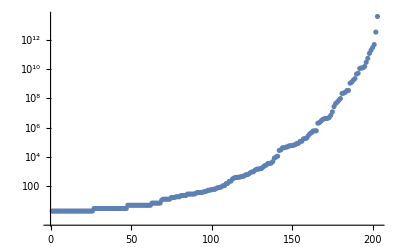

```mathematica
ListLogPlot[Map[First,l]//Sort]
```

```mathematica
TableForm[Table[{allGraphs[k,"graph"],With[{g=EmbedGraphInPlantri8[allGraphs,k]},{FactorInteger[Abs[ChromaticPolynomial[g,-1]]],FactorInteger[NumberOfSpanningTrees[g]]}]},{k,Take[atomKeys,3]}], TableDepth->3]
```

-Graphics- | {{2,4},{3,3},{5,1},{7,1},{11,1},{29,1},{467,1}}
{{7,1},{17,1},{61,1},{191,1},{6211,1},,}
-Graphics- | {{2,5},{3,2},{5,1},{11,1},{23,1},{863,1}}
{{13,1},{19,1},{269,1},{12263,1},,}
-Graphics- | {{2,3},{3,1},{11,2},{41,1},{59,1},{61,1}}
{{3,2},{11,1},{17,1},{53,1},{13931,1},}

```mathematica
TableForm[Table[{allGraphs[k,"graph"],With[{g=allGraphs[k,"graph"]},{Abs[ChromaticPolynomial[g,-1]],NumberOfSpanningTrees[g]}]},{k,{quad1Key,alfa1Key}}], TableDepth->3]
```

-Graphics- | {24}
{16}
-Graphics- | {6}
{3}

```mathematica
16
```

2 2^(1/3)